{{56.7009,1/200},{141.61,1/40},{495.508,9/250},{552.25,39/1000},{849.723,61/1000},{1416.02,99/1000}}

FittedModel[0.00651689+0.0000643255 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00651689 | 0.00381053 | 1.71023 | 0.162397
x | 0.0000643255 | 5.13742×10^-6 | 12.521 | 0.000234074

0.00651689+0.0000643255 x

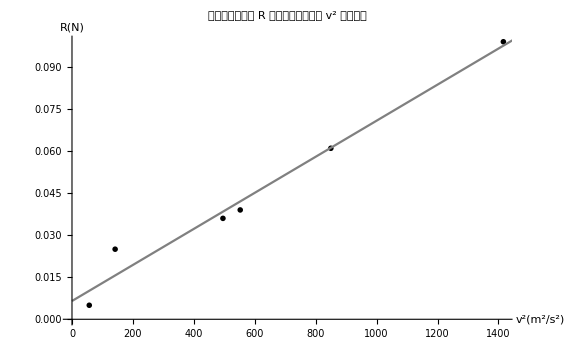

```mathematica
R = {5, 25, 36, 39, 61, 99} * 10^-3;
v = {7.53, 11.90, 22.26, 23.50, 29.15, 37.63};
v2 = v^2;
fitdata = Transpose[{v2,R}]
fit = LinearModelFit[fitdata,x,x]
%["ParameterTable"]
line = Fit[fitdata,{1,x},x]
Show[ListPlot[fitdata, PlotStyle->Black, PlotMarkers->{Style["X",10]}],
Plot[line,  {x,0,2000},PlotStyle->Gray],
AxesLabel->{Style["v^2(m^2/s^2)",15,Bold], Style["R(N)", 15, Bold]},
PlotLabel->Style["平板体所受流阻 R 与气体流速的平方 v^2 拟合直线",18,FontFamily->"Hack", Bold],
AxesStyle->Directive[Arrowheads[0.05],13],
ImageSize->Large]
```

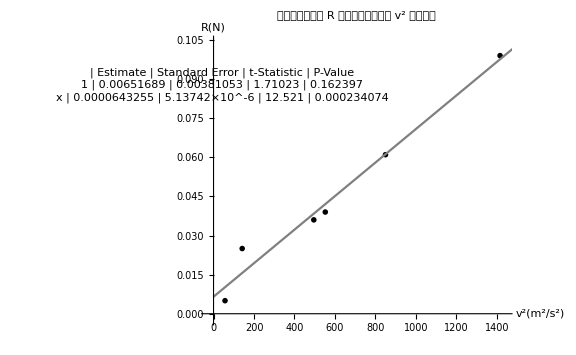

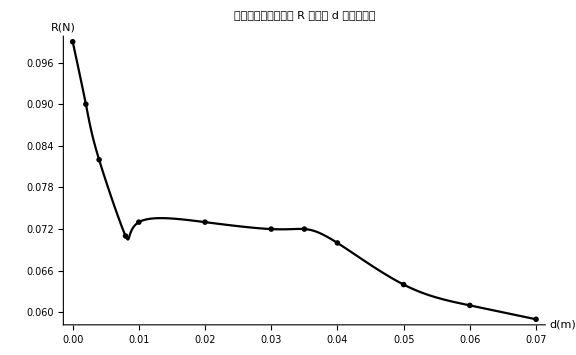

{{0.00001,37.9175},{0.002,36.0253},{0.004,34.2557},{0.008,31.6615},{1/100,32.1488},{1/50,32.1488},{3/100,31.9061},{0.035,31.9061},{1/25,31.415},{1/20,29.8936},{3/50,29.1031},{7/100,28.564}}

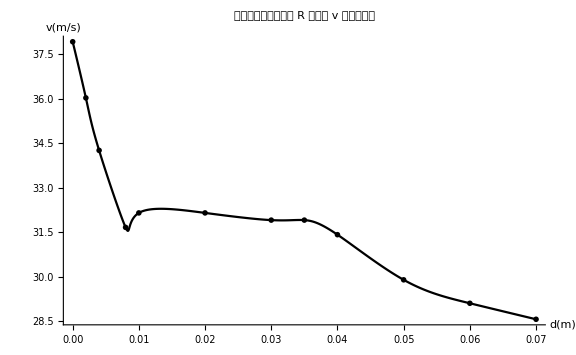

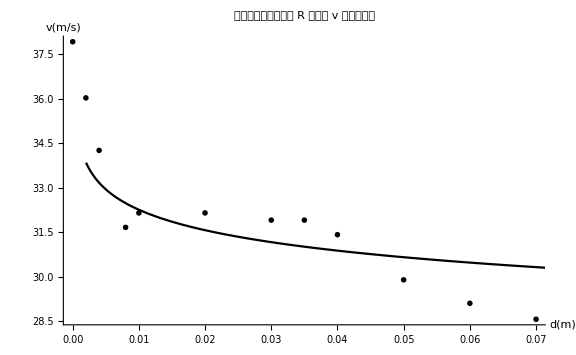

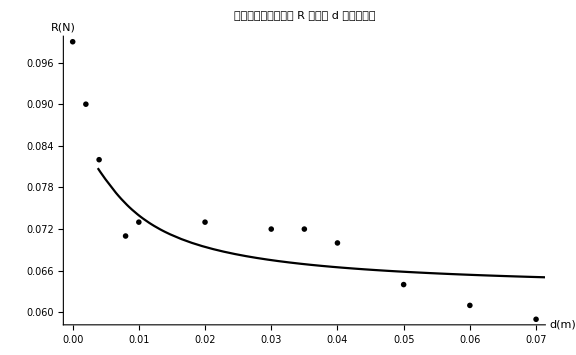

```mathematica
DeltaH = {0.001, 0.2, 0.4, 0.8, 1, 2, 3, 3.5, 4, 5, 6, 7} * 10^-2;
F = {99, 90, 82, 71, 73, 73, 72, 72, 70, 64, 61, 59} * 10^-3;
data = Transpose[{DeltaH, F}];
Show[ListPlot[data, PlotStyle->Black, Joined->True,InterpolationOrder->3],
ListPlot[data, PlotStyle->Black, PlotMarkers->{"X",10}],
AxesLabel->{Style["d(m)",15,Bold],Style["R(N)",15,Bold]},
PlotLabel->Style["平板测试物所受风阻 R 与距离 d 关系曲线图", 18, FontFamily->"Hack",Bold],
AxesStyle->Directive[Arrowheads[0.05],13],
ImageSize->Large]

Solve[y==line,x];
fx[x_] := -15545.943086848984*(0.006516887981847001-x);
t = fx[F];
anotherV = Sqrt[t];
theOtherData = Transpose[{DeltaH,anotherV}]
Show[ListPlot[theOtherData, PlotStyle->Black, Joined->True,InterpolationOrder->3],
ListPlot[theOtherData, PlotStyle->Black, PlotMarkers->{"X",10}],
AxesLabel->{Style["d(m)",15,Bold],Style["v(m/s)",15,Bold]},
PlotLabel->Style["平板测试物所受风阻 R 与风速 v 关系曲线图", 18, FontFamily->"Hack",Bold],
AxesStyle->Directive[Arrowheads[0.05],13],
ImageSize->Large]

theOtherLine=Fit[theOtherData,{1,x^-0.00001},x];
Show[ListPlot[theOtherData, PlotStyle->Black, PlotMarkers->{"X",10}],
Plot[theOtherLine,{x,0.0001,0.08}, PlotStyle->Black],
AxesLabel->{Style["d(m)",15,Bold],Style["v(m/s)",15,Bold]},
PlotLabel->Style["风速 v 与距离 h 关系曲线图", 18, FontFamily->"Hack",Bold],
AxesStyle->Directive[Arrowheads[0.05],13],
ImageSize->Large]


anotherfit = LinearModelFit[data,{x^-1,x^-2},x];
anotherline = Fit[data, {1,x^-1,x^-2,x^-3,x^-4},x];
Show[ListPlot[data, PlotStyle->Black, PlotMarkers->{"X",10}],
Plot[anotherline,{x,0.0001,0.08}, PlotStyle->Black],
AxesLabel->{Style["d(m)",15,Bold],Style["R(N)",15,Bold]},
PlotLabel->Style["平板测试物所受风阻 R 与距离 d 关系曲线图", 18, FontFamily->"Hack",Bold],
AxesStyle->Directive[Arrowheads[0.05],13],
ImageSize->Large]
```